## League of Legends: Metagame Network

### Who counters who? A first look.

#### http://www.counterstats.net

```mathematica
data=Drop[ImportString[Import["Champs.txt"],"Table"],1];
```

```mathematica
data2=Drop[ImportString[Import["Champions2.txt"],"Table"],1];
```

```mathematica
g=Join[Table[data[[i]][[2]]->data[[i]][[1]],{i,1,Length[data]}],Table[data2[[i]][[1]]->data2[[i]][[2]],{i,1,Length[data2]}]];
```

```mathematica
Graph[g,DirectedEdges->True,PlotRangePadding->0.1]
(*VertexRenderingFunction->(Text[#2,#1,Background->White]&)*)
```

-Graphics-

### In degree and Out degree

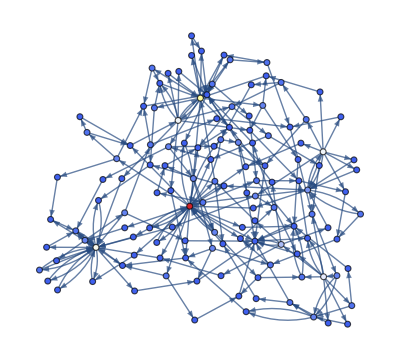

```mathematica
graph=Graph[g,VertexShapeFunction->"Circle",VertexSize->0.8,VertexLabels->Placed["Name",Tooltip]];
HighlighVertexDegree[g_,vd_]:=HighlightGraph[g,Table[Style[VertexList[g][[i]],ColorData["TemperatureMap"][vd[[i]]/Max[vd]]],{i,VertexCount[g]}]];
vd=VertexOutDegree[graph];
HighlighVertexDegree[graph,vd]
```

### Popularity, Win rates, and Ban rates

#### http://www.leagueofgraphs.com/champions/stats/platinum/by-winrate

```mathematica
stats=Import["ChampionStats"];
```

```mathematica
rates=Table[stats[[Position[stats,VertexList[graph][[i]]][[1]][[1]]]][[4]],{i,1,Length[VertexList[graph]]}];
```

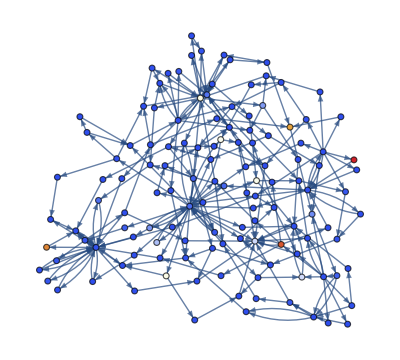

```mathematica
graph=Graph[g,VertexShapeFunction->"Circle",VertexSize->0.8,VertexLabels->Placed["Name",Tooltip]];
HighlighVertexDegree[g_,vd_]:=HighlightGraph[g,Table[Style[VertexList[g][[i]],ColorData["TemperatureMap"][vd[[i]]/Max[vd]]],{i,VertexCount[g]}]];
vd=rates;
HighlighVertexDegree[graph,vd]

(*for win rates
(vd[[i]]-Min[vd])/(Max[vd]-Min[vd])
*)
```

Between-ness can be interpreted as characters who move the story along. Basically, if you want to go from one character to another, they have to go through you first.
This isn’t the same as the most connected character.
How is the correlational structure related to the causal structure? What are those connections as a function of time?

For this project, the best thing to analyze first is the above states as a time series. It is how humans directly interact with the network by what they thing is the best strategy. Negative frequency dependent selection plays a role somehow here. How does the player’s knowledge of the current and past states change the states?

https://www.reddit.com/r/leagueoflegends/comments/31zsnr/riot_api_explained/